```mathematica
(*Feature Function*)
(*CRF State labels*)
f0[y_]:={KroneckerDelta[y,1],KroneckerDelta[y,2]};
```

```mathematica
(*One and two-body energies*)
Eone[yA_,tA_]:=tA. f0[yA];
Etwo[yA_,yB_,wAB_]:=f0[yA].wAB.f0[yB];
```

```mathematica
configEnergy[config_,edgesMat_,oneLgp_,twoLgp_]:=Module[
{i,numNodes, numEdges,eOne, eTwo},

numNodes=Length[config];

numEdges=Length[edgesMat];

(*Sum One-body energies (log node-potentials)*)
eOne=0;
For[i =1,i<=numNodes, i++,
eOne=eOne+Eone[config[[i]],oneLgp[[i]] ];
];

(*Sum Two-body energies (log edge-potentials)*)
eTwo=0;
For[i=1,i<=numEdges, i++,
eTwo=eTwo+Etwo[config[[  edgesMat[[i,1]]  ]],
                             config[[  edgesMat[[i,2]]  ]],
                             twoLgp[[i]] ];
];

Return[eOne + eTwo];
]
```

```mathematica
(*Graph specification*)
grp =Graph[{1<->2,1<->3, 2<->3},VertexLabels->"Name"];
nods=VertexList[grp];
edgMat=EdgeList[grp];
```

```mathematica
(*Node energies*)
tauA={Subscript[τ, Au]=Subscript[τ, A],Subscript[τ, Ad]=0};
tauB={Subscript[τ, Bu]=Subscript[τ, B],Subscript[τ, Bd]=0};
tauC={Subscript[τ, Cu]=Subscript[τ, C],Subscript[τ, Cd]=0};
tau ={tauA, tauB, tauC};
MatrixForm[tau];
```

```mathematica
(*Edge energies*)
omegaAB={{Subscript[ω, AuBu]=Subscript[ω, AB],Subscript[ω, AuBd]=0},
                {Subscript[ω, AdBu]=0,   Subscript[ω, AdBd]=Subscript[ω, AB]}};
omegaAC={{Subscript[ω, AuCu]=Subscript[ω, AC],Subscript[ω, AuCd]=0},
                {Subscript[ω, AdCu]=0,   Subscript[ω, AdCd]=Subscript[ω, AC]}};
omegaBC={{Subscript[ω, BuCu]=Subscript[ω, BC],Subscript[ω, BuCd]=0},
                {Subscript[ω, BdCu]=0,   Subscript[ω, BdCd]=Subscript[ω, BC]}};
omega={omegaAB,omegaAC,omegaBC};
MatrixForm[omega];
```

```mathematica
(*All configurations*)
X=Tuples[{1,2},3];
MatrixForm[X];
```

```mathematica
(*Test*)
configEnergy[X[[2]],edgMat,tau,omega]
```

τ_A+τ_B+ω_AB

```mathematica
(*All Boltzmann Weights*)
BW = Map[Exp[configEnergy[X[[#]],edgMat,tau,omega]]&, Range[ Length[X] ]   ];
TableForm[BW]
```

ⅇ^(τ_A+τ_B+τ_C+ω_AB+ω_AC+ω_BC)
ⅇ^(τ_A+τ_B+ω_AB)
ⅇ^(τ_A+τ_C+ω_AC)
ⅇ^(τ_A+ω_BC)
ⅇ^(τ_B+τ_C+ω_BC)
ⅇ^(τ_B+ω_AC)
ⅇ^(τ_C+ω_AB)
ⅇ^(ω_AB+ω_AC+ω_BC)

```mathematica
(*Partition Function*)
Total[BW]
```

ⅇ^(τ_A+τ_B+ω_AB)+ⅇ^(τ_C+ω_AB)+ⅇ^(τ_B+ω_AC)+ⅇ^(τ_A+τ_C+ω_AC)+ⅇ^(τ_A+ω_BC)+ⅇ^(τ_B+τ_C+ω_BC)+ⅇ^(ω_AB+ω_AC+ω_BC)+ⅇ^(τ_A+τ_B+τ_C+ω_AB+ω_AC+ω_BC)

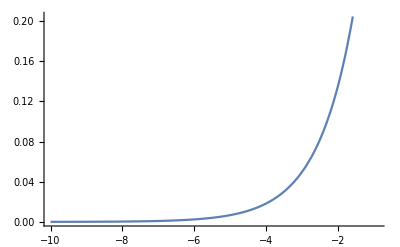

```mathematica
Plot[ⅇ^x,{x,-10,-0.9}]
```